```mathematica
(*https://tali.link/posts/random-walks/*)
```

```mathematica
RandomWalk[timesteps_]:=FoldList[Plus,0,RandomChoice[{1,1,1}->{-1,0,1},timesteps]];
```

```mathematica
ListLinePlot[RandomWalk[500],PlotStyle->Blue,AxesLabel->{"Étapes","Position"},PlotLabel->"Marche Aléatoire (1D)"]
```

```mathematica
Distribution[length_,n_]:=With[{width=2.2 Sqrt[length]},BinCounts[#,{-width,width,1}]&/@Transpose[Table[RandomWalk[length],{n}]]];
```

```mathematica
ArrayPlot[Distribution[50,1]]
```

-Graphics-

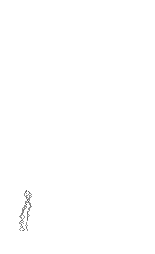
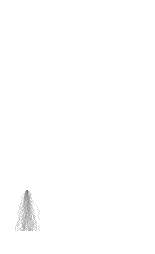
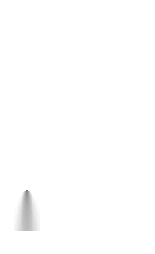

```mathematica
Row[Labeled[ArrayPlot[Sqrt@Distribution[50,#],PixelConstrained->5],Row@{"n = ",#}]&/@{5,50,5000}]
```